```mathematica
intervalTestOG=(N[1*((1.8/1)^(1/15))^Range[15]]-1)/0.95
```

{0.042067,0.0858152,0.131312,0.178626,0.227832,0.279004,0.332221,0.387565,0.44512,0.504976,0.567224,0.631959,0.699282,0.769294,0.842105}

```mathematica
intervalTest=(0.8421052631578968-intervalTestOG)
```

{0.800038,0.75629,0.710794,0.663479,0.614273,0.563101,0.509884,0.45454,0.396985,0.337129,0.274882,0.210146,0.142824,0.0728108,0.}

```mathematica
intervalTest=-(0.042067018654506495-Reverse@(N[1*((1.8/1)^(1/15))^Range[15]]-1)/0.95)
```

{0.800038,0.727227,0.657215,0.589892,0.525157,0.462909,0.403053,0.345498,0.290154,0.236937,0.185765,0.136559,0.0892447,0.0437482,0.}

```mathematica
intervalTest=0.8-Range[0,0.8,.8/14]
```

{0.8,0.742857,0.685714,0.628571,0.571429,0.514286,0.457143,0.4,0.342857,0.285714,0.228571,0.171429,0.114286,0.0571429,1.11022×10^-16}

```mathematica
GrayLevel[(0.8)]
```

GrayLevel[0.8]

```mathematica
cellularAutomata4Levels=(0.8421052631578968-(N[1*((1.8/1)^(1/15))^Range[15]]-1)/0.95);
```

```mathematica
Manipulate[
If[cellularAutomata4==0,Graphics[],
Graphics[{
Table[{GrayLevel[(intervalTest[[i]])],
PointSize[0.0135],
Point[If[cellularAutomata4≤Length@cellularAutomata4Points[[i]],cellularAutomata4Points[[i,1;;cellularAutomata4]],cellularAutomata4Points[[i,1;;Length@cellularAutomata4Points[[i]]]]]]},{i,1,Length@intervalTest}]
},PlotRange->{{0,71},{0,71}}]],
{{cellularAutomata4,0,Style["Cellular Automata 4",Italic]},0,Length@cellularAutomata4Points[[5]],1,ControlPlacement->Top,Manipulator,ImageSize->Large}]
```

```mathematica
Length@cellularAutomata4Levels
```

15

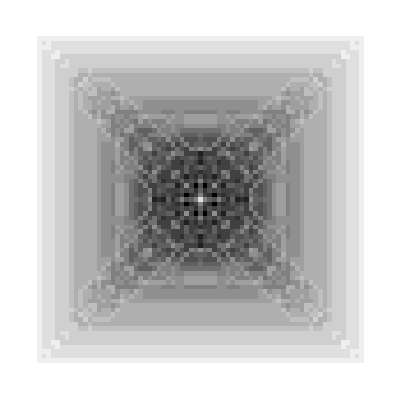

```mathematica
ArrayPlot@Mean[CellularAutomaton[{14, {2, 1}, {1, 1}},{{{1}},0},35]]
```

```mathematica
(Position[#,1]&/@CellularAutomaton[{14, {2, 1}, {1, 1,1}},{{{{1}}},0},10])
```

```mathematica
-Graphics--Graphics--Graphics-
```

Part::take: Cannot take positions -1 through -4 in {«1»}.

General::stop: Further output of Part::take will be suppressed during this calculation.